{a→0.0232174,b→-0.298527}

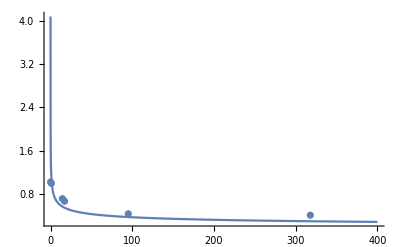

```mathematica
z=a+x^b;
f=FindFit[{{0.00218,6.387230},{1,1},{317.83,9.9250/24},{95.162,10.5433/24},{14.536,0.71833},{17.147,0.6713},{0.107,1.025957}},z,{a,b},x]
Show[Plot[(z+0.1)/.f,{x,0.01,400},PlotRange->Full],ListPlot[{{1,1},{317.83,9.9250/24},{95.162,10.5433/24},{14.536,0.71833},{17.147,0.6713},{0.107,1.025957},{0.055,58.646}}]]
```

```mathematica
(z/.f)/.x->0.00218
```

6.254

```mathematica
(z/.f)/.x->0.815
```

1.08619

```mathematica
(1+1^1)/2
```

1

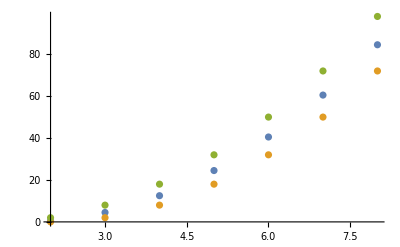

```mathematica
DiscretePlot[{2(x-3/2)^2,2(x-3/2-1/2)^2,2(x-3/2+1/2)^2},{x,2,8},Filling->None]
```

```mathematica
{2(x-3/2)^2,2(x-3/2-1/2)^2,2(x-3/2+1/2)^2}/.x->0
```

{9/2,8,2}

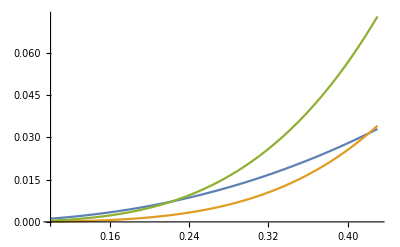

```mathematica
Plot[{0.23*m^2.3,m^4,1.4*m^3.5},{m,0.1,0.43}]
```

```mathematica
Plot[(4Pi*R^2*T^4)/.R->1000,{T,2100,78400}]
```

-Graphics-

```mathematica
4Pi*5.67*10^(-8)*696340000^2*5770^4
```

3.82947×10^26

```mathematica
16Pi*5.67*10^(-8)*1.496*10^11
```

426368.

```mathematica
0.1485@1
24.2@95
```

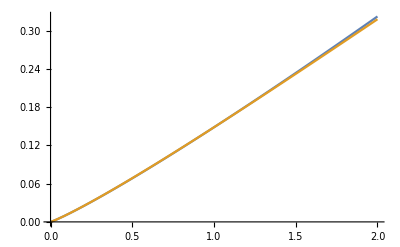

```mathematica
Plot[{0.1485a^1.1185,0.1485a^(1.1185-Log[1+a/100])},{a,0,2}]
```

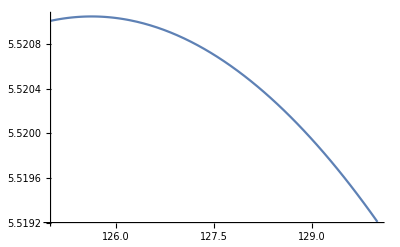

```mathematica
Plot[{0.1485a^(1.1185-Log[1+0.04Sqrt[a]])},{a,125,130}]
```

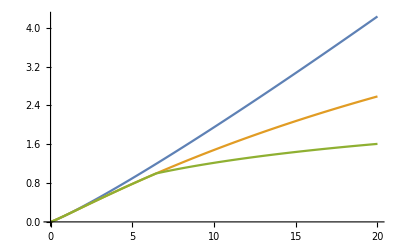

```mathematica
z=0.1485a^(1.1185-Log[1+0.04Sqrt[a]]);
Plot[{0.1485a^1.1185,z,If[z>1,Sqrt[z],z]},{a,0,20}]
```

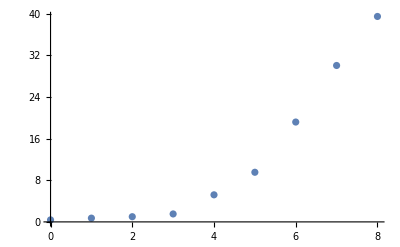

```mathematica
ListPlot[{{0,0.3871},{1,0.7233},{2,1},{3,1.5273},{4,5.2028},{5,9.5388},{6,19.1914},{7,30.0611},{8,39.482}}]
```

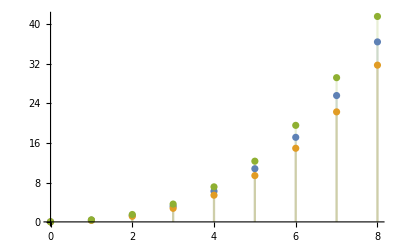

```mathematica
DiscretePlot[{0.05(i+1)^3,0.05(0.955(i+1))^3,0.05(1.045(i+1))^3},{i,0,8},PlotRange->All]
```

```mathematica
0.5*(0.2)^(1/2)
```

0.223607

```mathematica
0.5*(200.0)^(1/2)
```

7.07107

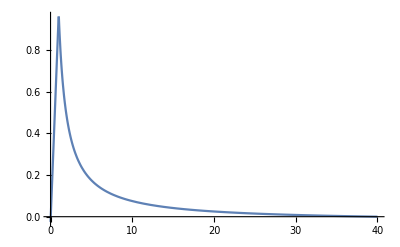

```mathematica
Plot[Min[x/1-1/40,1/x-1/40],{x,0,40},PlotRange->All]
```

```mathematica
FindFit[{{1/50,0.95*300},{1,0.95*372},{50,0.95*560}},a+b*Log[c*x]^2,{a,b,c},x]
```

{a→284.197,b→3.60038,c→80.1711}

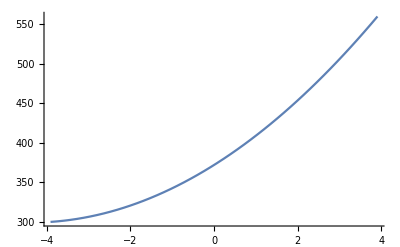

```mathematica
Plot[299.1551724137931+3.7898776822828513*Log[80.17114907882885Exp[P]]^2,{P,Log[1/50],Log[50]}]
```

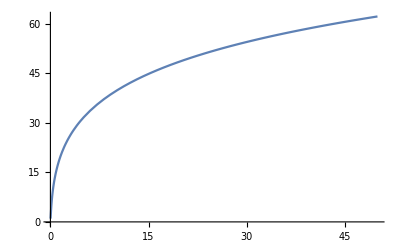

```mathematica
Plot[1+Log[50*P]^2,{P,1/50,50}]
```

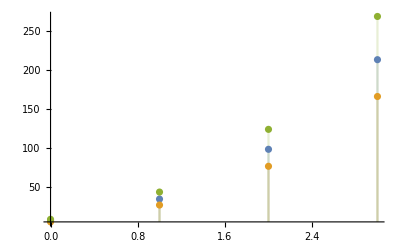

```mathematica
DiscretePlot[{2.5(i+1.4)^3,2.5(0.92(i+1.4))^3,2.5(1.08(i+1.4))^3},{i,0,3},PlotRange->All]
```

```mathematica
{2.5(i+1.4)^3,2.5(0.92(i+1.4))^3,2.5(1.08(i+1.4))^3}/.i->0
```

{6.86,5.3418,8.64162}